## Reading data

```mathematica
data={{1,2,3,4},{5,6,7,8},{9,10,11,12}};
```

```mathematica
RawGyroTime=Import["/home/work/local/working/my_stuff/chapchom/private/julio/dead_reckoning/RESLT/raw_gyro.dat"];
```

```mathematica
RawGyroTimeTable=Table[{RawGyroTime[[i,1]],RawGyroTime[[i,2]] 180.0/π},{i,1,7370}];
```

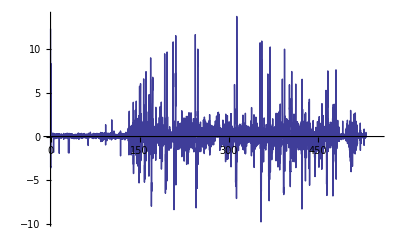

```mathematica
ListLinePlot[RawGyroTimeTable, PlotRange->{{0,550},All}]
```